```mathematica
Nat=10000;   "This is the number of atoms";
Chi=0.0005;    "Two-body interaction strenght";

DelA[t_]:= Nat*Chi/2;
DelB[t_]:=-Nat*Chi/2;

Diaggon[n1_]      :=Chi*(Nat*n1+Nat/2-2*(n1)^2)+(DelB[t]-DelA[t])*(Nat/4-n1);
ElemRight[n1_] :=-Chi*(Nat/2-n1)*(n1+1);
ElemLeft[n1_]   :=-Chi*(Nat/2-n1+1)*n1;

"Initialize the matrix C";

InitiMatC=SparseArray[{{Nat/2+1,Nat/2+1}->0,{1,1}->Diaggon[0],{1,2}->ElemRight[0]}];
InitiMatC+=SparseArray[{{Nat/2+1,Nat/2+1}->0,{Nat/2+1,Nat/2+1}->Diaggon[Nat/2],{Nat/2+1,Nat/2}->ElemLeft[Nat/2]}];
InitiMatC+=Sum[SparseArray[{{Nat/2+1,Nat/2+1}->0,{i,i}->Diaggon[i-1],{i,i+1}->ElemRight[i-1],{i,i-1}->ElemLeft[i-1]}],{i,2,Nat/2}];

"Right hand side dt C=-I*M(t)C";

RHS=-I*InitiMatC.Table[C[i][t],{i,Nat/2+1}];
```

```mathematica
diffEqs=Table[C[i]'[t]==RHS[[i]],{i,Nat/2+1}];
"Initial conditions: in the reduced Dicke manifold we find that the initial conditions are (recall that in Mathematica we start to count from 1 instead of 0, so the representative element of the index=0 is equal to 1) for our system psi=|0>^{N/2}|1>^{N/2}, equal to C1(0)=1 and 0 otherwise";

initCond=Table[KroneckerDelta[i,1],{i,Nat/2+1}];
vars=Table[C[i][t],{i,Nat/2+1}];

initCondF
```

{C[1][0]==1,C[2][0]==0,C[3][0]==0,C[4][0]==0,C[5][0]==0,C[6][0]==0,C[7][0]==0,C[8][0]==0,C[9][0]==0,C[10][0]==0,C[11][0]==0,C[12][0]==0,C[13][0]==0,C[14][0]==0,C[15][0]==0,C[16][0]==0,C[17][0]==0,C[18][0]==0,C[19][0]==0,C[20][0]==0,C[21][0]==0,4959,C[4981][0]==0,C[4982][0]==0,C[4983][0]==0,C[4984][0]==0,C[4985][0]==0,C[4986][0]==0,C[4987][0]==0,C[4988][0]==0,C[4989][0]==0,C[4990][0]==0,C[4991][0]==0,C[4992][0]==0,C[4993][0]==0,C[4994][0]==0,C[4995][0]==0,C[4996][0]==0,C[4997][0]==0,C[4998][0]==0,C[4999][0]==0,C[5000][0]==0,C[5001][0]==0}
 |  |  |  |

```mathematica
initCondF=Table[ C[i][0]==initCond[[i]],{i,Nat/2+1} ];
```

```mathematica
SolutionSys=NDSolveValue[Flatten[Join[diffEqs,initCondF]],vars,{t,0.1}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],4986,InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}
 |  |  |  |

General::munfl: (6.00152×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.47068×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.6032×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

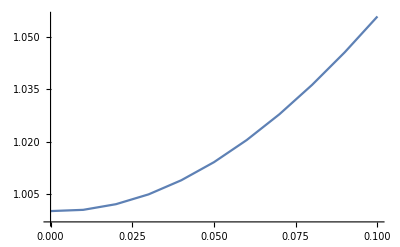

```mathematica
data=Table[{τ, Sum[n Abs[SolutionSys[[n]]^2]/.t->τ,{n,5001}]},{τ,0,0.1,0.01}];
ListLinePlot[data]
```

```mathematica
Sinh[Nat*Chi*0.1/2]^2
```

0.063813

```mathematica
Sum[Abs[SolutionSys[[n]]^2]/.t->0.1,{n,5001}]
```

General::munfl: (5.42939×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.22395×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.75865×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.997462